# Kets, Bras, Operators and Bases

Malcolm Levitt & Christian Bengs 01-July-2023
This documentation applies to SpinDynamica v3.10

SpinDynamica provides routines for defining and manipulating kets, bras, operators and Hilbert space bases. Specific routines for angular momentum operators, rotation operators, spherical tensor operators, single-transition operators, and spin-exchange operators are provided.

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
```

## Ket

The quantum mechanical ket |ψ> describing the state of a nuclear spin system is defined using the symbol Ket.

The general syntax is Ket[{{j,M_j},{k,M_k}..}, spinsystem] where eigensystem has the syntax {{j,I_j},{k,I_k}..} and defines the labels for the spins {j,k,..} and their angular momentum quantum numbers {I_j,I_k..}. If spinsystem is absent the current spin system is assumed.

There are various abbreviated forms for Ket which are explained below.

### single spin-1/2

In the case of spin-1/2, the symbols α and β denote M_j=±1/2.

For example, consider a single spin-1/2, with label 1:

```mathematica
SetSpinSystem[1]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

In the line below, the Ket is defined using the full general form. The routines automatically present the result using  Dirac notation:

```mathematica
Ket[{{1,1/2}},{{1,1/2}}]
```

|α⟩

The same result is obtained when the spinsystem definition is omitted, since the current SpinSystem[] is used:

```mathematica
Ket[{{1,1/2}}]
```

|α⟩

The α and β symbols may also be used to input the Ket:

```mathematica
Ket["α"]
```

|α⟩

similarly:

```mathematica
Ket["β"]
```

|β⟩

### several spins-1/2

When there are two or more spins-1/2, the Kets may be defined by using strings of “α” and “β” characters:

```mathematica
SetSpinSystem[3]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

```mathematica
Ket["αβα"]
```

|αβα⟩

The same result is obtained by defining the quantum numbers explicitly:

```mathematica
Ket[{{1,1/2},{2,-1/2},{3,1/2}}]
```

|αβα⟩

### spins > 1/2

When one or more spins is more than 1/2, the “α” and “β” symbols are not appropriate. Full specifications must be given.

For example, consider a single spin-1, with label “I”.

```mathematica
SetSpinSystem[{{"I",1}}]
```

SetSpinSystem::set: the spin system has been set to {{I,1}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1}},BasisLabels→Automatic].

The Ket must be inputted explicitly in this case:

```mathematica
Ket[{{"I",1}}]
```

|1+1⟩

Now consider a spin-1 nucleus “I” coupled to a spin-3/2 nucleus “S”:

```mathematica
SetSpinSystem[{{"I",1},{"S",3/2}}]
```

SetSpinSystem::set: the spin system has been set to {{I,1},{S,3/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1},{S,3/2}},BasisLabels→Automatic].

to define a Ket, you must specify the name of the nucleus and its M-value.

```mathematica
Ket[{{"I",0},{"S",-1/2}}]
```

|10,3/2-1/2⟩

### MagneticQuantumNumber

The routine MagneticQuantumNumber may be applied to a Ket to obtain the total magnetic quantum number (M-value) of the ket, either for all of the spins, or for one or more subsets. Consider, for example, the following Ket in a 4-spin-1/2 system

```mathematica
SetSpinSystem[4];
ket =Ket["αβαα"]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

|αβαα⟩

The total M-value is calculated as follows:

```mathematica
MagneticQuantumNumber[ket]
```

1

The M-value for only the first 3 spins is calculated as follows:

```mathematica
MagneticQuantumNumber[ket,{1,2,3}]
```

1/2

A list of M-values for the first the two spins, and the last two, is calculated as follows:

```mathematica
MagneticQuantumNumber[ket,{{1,2},{3,4}}]
```

{0,1}

If a ket contains a mixture of M-values, a list of the corresponding values is returned:

```mathematica
ket=(Ket["αββα"]+Ket["βααβ"])/Sqrt[2]
```

(|βααβ⟩+|αββα⟩)/(√2)

```mathematica
MagneticQuantumNumber[ket]
MagneticQuantumNumber[ket,{1,2,3}]
MagneticQuantumNumber[ket,{{1,2},{3,4}}]
MagneticQuantumNumber[ket,{{1},{2},{3}}]
```

0

{-1/2,1/2}

{0,0}

{{-1/2,1/2},{-1/2,1/2},{-1/2,1/2}}

### trapping inappropriate arguments

By default, the routine checks for inappropriate arguments. 
In the case below the Ket is defined using a spin that is not in the current spin system:

```mathematica
SetSpinSystem[2]
Ket[{{"I",1/2},{"S",-1/2}}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Ket::invalidspins: The following spins do not belong to the requested spin system: {I,S}

$Failed

The problem is corrected by defining the spin system beforehand:

```mathematica
SetSpinSystem[{{"I",1/2},{"S",1/2}}]
Ket[{{"I",1/2},{"S",-1/2}}]
```

SetSpinSystem::set: the spin system has been set to {{I,1/2},{S,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1/2},{S,1/2}},BasisLabels→Automatic].

|αβ⟩

In the cases below an invalid magnetic quantum number is used

```mathematica
SetSpinSystem[2];
Ket[{{1,1/2},{2,0}}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Ket::invalidm: the following pairs of spins and magnetic quantum numbers are invalid: {{2,0}}

$Failed

```mathematica
SetSpinSystem[{{"I",1},{"S",3/2}}]
Ket[{{"I",0},{"S",-5/2}}]
```

SetSpinSystem::set: the spin system has been set to {{I,1},{S,3/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1},{S,3/2}},BasisLabels→Automatic].

Ket::invalidm: the following pairs of spins and magnetic quantum numbers are invalid: {{S,-5/2}}

$Failed

### ProductKet

The direct product of kets for different sets of spins may be constructed using ProductKet

For example, the product ket of |α> for spin #1 and |β> for spin #2 may be constructed as follows:

```mathematica
SetSpinSystem[2];ProductKet[Ket["α",{{1,1/2}}],Ket["β",{{2,1/2}}]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

|αβ⟩

The ProductKet may also be taken for superposition kets:

```mathematica
ProductKet[
Ket["α",{{1,1/2}}],
(Ket["α",{{2,1/2}}]+I Ket["β",{{2,1/2}}])/Sqrt[2]
]
```

(ⅈ |αβ⟩+|αα⟩)/(√2)

## Bra

Bras work exactly the same as Kets, for example

```mathematica
SetSpinSystem[{{"I",1},{"S",3/2}}]
Bra[{{"I",0},{"S",-1/2}}]
```

SetSpinSystem::set: the spin system has been set to {{I,1},{S,3/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1},{S,3/2}},BasisLabels→Automatic].

<10,3/2-1/2|

## Bra.Ket

The Dirac bracket is calculated by using Dot (“.”).

The BraKet of a state with itself evaluates to unity:

```mathematica
SetSpinSystem[2]
Bra["αβ"].Ket["αβ"]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

1

The BraKet between different states evaluates to zero :

```mathematica
Bra["αβ"].Ket["αα"]
```

0

Note that Ket.Bra is not the same as Bra.Ket:

```mathematica
Ket["αβ"].Bra["αα"]
```

|αβ⟩.<αα|

## Bases

In SpinDynamica, bases are sets of orthogonal kets, used to define the Hilbert space for spin dynamical calculations. There are several built-in bases, and it is also possible to define bases oneself.

### General Basis routines

#### SetBasis

SetBasis is used to set the working basis for spin-dynamical calculations. By default, the working basis is set to be the Zeeman basis when SetSpinSystem is used:

```mathematica
SetSpinSystem[3]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

It is also possible to set the working basis explicitly:

```mathematica
SetBasis[ZeemanBasis[]]
```

SetBasis::alreadyset: The basis is already set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]. No action has been taken.

#### Basis

Executing Basis[] reveals the current working basis:

```mathematica
Basis[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

#### BasisDimension

BasisDimension[basis] gives the dimension of a given basis.

```mathematica
BasisDimension[ZeemanBasis[{{1,1/2}}]]
```

2

If the argument is missing, the current basis is assumed.

```mathematica
Basis[]
BasisDimension[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

8

#### BasisKets

BasisKets[basis] gives the basis kets for a given basis:

```mathematica
BasisKets[ZeemanBasis[{{1,1/2}}]]
```

{|α⟩,|β⟩}

If the argument is missing, the current basis is assumed

```mathematica
Basis[]
BasisKets[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

{|ααα⟩,|βαα⟩,|αβα⟩,|ββα⟩,|ααβ⟩,|βαβ⟩,|αββ⟩,|βββ⟩}

#### BasisBras

BasisBras[basis] gives the basis bras for a given basis:

```mathematica
BasisBras[ZeemanBasis[{{1,1/2}}]]
```

{<α|,<β|}

If the argument is missing, the current basis is assumed.

```mathematica
Basis[]
BasisBras[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

{<ααα|,<βαα|,<αβα|,<ββα|,<ααβ|,<βαβ|,<αββ|,<βββ|}

#### BasisLabels

It is possible to refer to the Kets and Bras of a given basis using labels. By default, these labels are simply given by the integers {1,2,..}, up to the BasisDimension

```mathematica
BasisLabels[ZeemanBasis[{{1,1/2}}]]
```

{1,2}

If the argument is missing, the current basis is assumed

```mathematica
Basis[]
BasisLabels[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

{1,2,3,4,5,6,7,8}

Any ket or bra of a given basis may be specified by using its label, rather than explicitly

```mathematica
Basis[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

```mathematica
Ket[5]
```

|ααβ⟩

```mathematica
Bra[6]
```

<βαβ|

### ZeemanBasis

The default basis in SpinDynamica is the ZeemanBasis. The general syntax is ZeemanBasis[spinsystem,options]. The set of rules options may contain a definition for BasisLabels.

For example, consider a two-spin-1/2 system:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

The working basis is automatically set to the ZeemanBasis:

```mathematica
Basis[]
```

ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic]

Here are the BasisKets of this basis:

```mathematica
BasisKets[]
```

{|αα⟩,|βα⟩,|αβ⟩,|ββ⟩}

With BasisLabels→Automatic, these kets are numbered in sequence:

```mathematica
Ket[1]
```

|αα⟩

```mathematica
Ket[3]
```

|αβ⟩

similarly for the Bras:

```mathematica
Bra[2]
```

<βα|

It is possible to define a different set of BasisLabels, which can be pretty much anything:

```mathematica
newbasis=ZeemanBasis[BasisLabels->{"a","b","c",3}]
```

ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→{a,b,c,3}]

After setting the working basis, the kets and bras of this basis may be referenced using these user-defined labels:

```mathematica
SetBasis[newbasis]
Ket["a"]
```

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→{a,b,c,3}].

|αα⟩

```mathematica
Bra["b"].Ket["b"]
Bra["b"].Ket[3]
```

1

0

The label must belong to the set of BasisLabels:

```mathematica
Bra["e"]
```

Bra::inappbl: inappropriate basis label

$Failed

#### alternative Zeeman basis ordering

The default ordering of the ZeemanBasis kets in SpinDynamica differs slightly from that in the book “Spin Dynamics” and some other software packages such as SIMPSON and SPINEVOLUTION. A basis state ordering which is compatible with the “Spin Dynamics” book may be imposed by using DefineBasis (described below).

### SingletTripletBasis

The SingletTripletBasis is defined for the case of two spins-1/2:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

```mathematica
SetBasis[SingletTripletBasis[]]
```

SetBasis::set: the state basis has been set to SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

The basis kets are given by the singlet state and the three triplet states:

```mathematica
BasisKets[]
```

{(-|βα⟩+|αβ⟩)/(√2),|αα⟩,(|βα⟩+|αβ⟩)/(√2),|ββ⟩}

```mathematica
BasisBras[]
```

{(-<βα|+<αβ|)/(√2),<αα|,(<βα|+<αβ|)/(√2),<ββ|}

By default, the basis kets are labelled {1,2,3,4}:

```mathematica
BasisLabels[]
```

{1,2,3,4}

This may be superseded, if desired, by a more informative labelling:

```mathematica
SetBasis[SingletTripletBasis[BasisLabels->{"S_0","T_(+1)","T_0","T_-1"}]]
```

SetBasis::set: the state basis has been set to SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→{S_0,T_(+1),T_0,T_-1}].

The Kets and Bras may now be referenced using these symbols:

```mathematica
Ket["S_0"]
```

(-|βα⟩+|αβ⟩)/(√2)

```mathematica
Bra["T_0"]
```

(<βα|+<αβ|)/(√2)

### Eigenbasis

An eigenbasis of an arbitrary hermitian operator may be defined using Eigenbasis. In the example below, the basis is set to the eigenbasis of the I_x operator, for a single spin-1/2:

```mathematica
SetSpinSystem[1];
SetBasis[Eigenbasis[opI["x"]]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

CheckBasis::orthonormal: State basis is orthonormal.

SetBasis::set: the state basis has been set to Eigenbasis[I_(1x),{{1,1/2}},CheckOperatorType→False,BasisLabels→Automatic,TargetBasis→None].

The kets of the eigenbasis are superpositions of the α and β spin states:

```mathematica
BasisKets[]
```

{0.707107 |β⟩-0.707107 |α⟩,0.707107 |β⟩+0.707107 |α⟩}

```mathematica
BasisBras[]
```

{0.707107 <β|-0.707107 <α|,0.707107 <β|+0.707107 <α|}

```mathematica
Ket[1]
```

0.707107 |β⟩-0.707107 |α⟩

```mathematica
Bra[1].Ket[1]
```

1.

#### TargetBasis

The ordering of the kets in an eigenbasis may be controlled by using the TargetBasis option. Specifying TargetBasis→tbasis ensures that the kets of the eigenbasis are ordered so as to give a best possible match to the basis tbasis.

For example, consider a 2-spin-1/2 system, with the Hamiltonian defined below:

```mathematica
SetSpinSystem[2]
H = 2π 100 opI[1].opI[2]+2π 10 (opI[1,"z"]-opI[2,"z"])
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

200 π ((I⃗)_1•(I⃗)_2)+20 π (I_(1z)-I_(2z))

Suppose we wish to define the eigenbasis of this Hamiltonian. In general, the basis kets of this eigenbasis are generated in no particular order:

```mathematica
BasisKets[Eigenbasis[H]]
```

{0.773342 |βα⟩-0.633989 |αβ⟩,0.633989 |βα⟩+0.773342 |αβ⟩,1. |αα⟩,1. |ββ⟩}

We can specify that the ordering of the eigenbasis kets should be as close as possible to those of the SingletTripletBasis as follows:

```mathematica
DefineBasis[basis,
Eigenbasis[H, TargetBasis->SingletTripletBasis[]]
]
```

CheckBasis::orthonormal: State basis is orthonormal.

DefineBasis::defined: The state basis basis has been defined. To use this basis, execute SetBasis[basis].

```mathematica
BasisKets[basis]
```

{-0.773342 |βα⟩+0.633989 |αβ⟩,1. |αα⟩,0.633989 |βα⟩+0.773342 |αβ⟩,1. |ββ⟩}

Note that the kets are now ordered so that the first ket is similar to the singlet state, and the remaining kets are similar (or identical) to those of the triplet states:

```mathematica
BasisKets[SingletTripletBasis[]]
```

{(-|βα⟩+|αβ⟩)/(√2),|αα⟩,(|βα⟩+|αβ⟩)/(√2),|ββ⟩}

### ProductBasis

The direct product of two bases may be generated using ProductBasis. In the example below, the basis is set to the product of the SingletTripletBases for the spin pair {1,2} and the ZeemanBasis for spin 3:

```mathematica
SetSpinSystem[3];
SetBasis[
ProductBasis[SingletTripletBasis[{1,2}],ZeemanBasis[{3}]]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

CheckBasis::orthonormal: State basis is orthonormal.

SetBasis::set: the state basis has been set to ProductBasis[{SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic],ZeemanBasis[{{3,1/2}},BasisLabels→Automatic]},{{1,1/2},{2,1/2},{3,1/2}},Validity→True].

The basis kets are the products of the singlet-triplet kets for spins #1 and #2, and the Zeeman state for spin #3.

```mathematica
BasisKets[]
```

{(-|βαα⟩+|αβα⟩)/(√2),|ααα⟩,(|βαα⟩+|αβα⟩)/(√2),|ββα⟩,(-|βαβ⟩+|αββ⟩)/(√2),|ααβ⟩,(|βαβ⟩+|αββ⟩)/(√2),|βββ⟩}

```mathematica
BasisBras[]
```

{(-<βαα|+<αβα|)/(√2),<ααα|,(<βαα|+<αβα|)/(√2),<ββα|,(-<βαβ|+<αββ|)/(√2),<ααβ|,(<βαβ|+<αββ|)/(√2),<βββ|}

The product of any number of bases may be taken. The example below takes the product of the ZeemanBasis for spin #1 with the Singlet-Triplet basis for spins #2 and #3, and the Singlet-Triplet basis for spins #4 and #5:

```mathematica
SetSpinSystem[5];
SetBasis[
ProductBasis[
ZeemanBasis[{1}],
SingletTripletBasis[{2,3}],
SingletTripletBasis[{4,5}]
]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2}},BasisLabels→Automatic].

CheckBasis::orthonormal: State basis is orthonormal.

SetBasis::set: the state basis has been set to ProductBasis[{ZeemanBasis[{{1,1/2}},BasisLabels→Automatic],SingletTripletBasis[{{2,1/2},{3,1/2}},BasisLabels→Automatic],SingletTripletBasis[{{4,1/2},{5,1/2}},BasisLabels→Automatic]},{«1»},Validity→True].

```mathematica
BasisKets[]
```

{1/2 (|αβαβα⟩-|αβααβ⟩-|ααββα⟩+|ααβαβ⟩),1/2 (|ββαβα⟩-|ββααβ⟩-|βαββα⟩+|βαβαβ⟩),(-|αααβα⟩+|ααααβ⟩)/(√2),(-|βααβα⟩+|βαααβ⟩)/(√2),1/2 (-|αβαβα⟩+|αβααβ⟩-|ααββα⟩+|ααβαβ⟩),1/2 (-|ββαβα⟩+|ββααβ⟩-|βαββα⟩+|βαβαβ⟩),(-|αβββα⟩+|αββαβ⟩)/(√2),(-|ββββα⟩+|βββαβ⟩)/(√2),(-|αβααα⟩+|ααβαα⟩)/(√2),(-|ββααα⟩+|βαβαα⟩)/(√2),|ααααα⟩,|βαααα⟩,(|αβααα⟩+|ααβαα⟩)/(√2),(|ββααα⟩+|βαβαα⟩)/(√2),|αββαα⟩,|βββαα⟩,1/2 (-|αβαβα⟩-|αβααβ⟩+|ααββα⟩+|ααβαβ⟩),1/2 (-|ββαβα⟩-|ββααβ⟩+|βαββα⟩+|βαβαβ⟩),(|αααβα⟩+|ααααβ⟩)/(√2),(|βααβα⟩+|βαααβ⟩)/(√2),1/2 (|αβαβα⟩+|αβααβ⟩+|ααββα⟩+|ααβαβ⟩),1/2 (|ββαβα⟩+|ββααβ⟩+|βαββα⟩+|βαβαβ⟩),(|αβββα⟩+|αββαβ⟩)/(√2),(|ββββα⟩+|βββαβ⟩)/(√2),(-|αβαββ⟩+|ααβββ⟩)/(√2),(-|ββαββ⟩+|βαβββ⟩)/(√2),|αααββ⟩,|βααββ⟩,(|αβαββ⟩+|ααβββ⟩)/(√2),(|ββαββ⟩+|βαβββ⟩)/(√2),|αββββ⟩,|βββββ⟩}

### DefineBasis and UndefineBasis

#### DefineBasis

It is also possible to define one’s own basis, using any orthonormal set of Kets.

```mathematica
SetSpinSystem[1];
DefineBasis[userbasis,{(Ket["α"]+I Ket["β"])/Sqrt[2],(Ket["α"]-I Ket["β"])/Sqrt[2]}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

CheckBasis::orthonormal: State basis is orthonormal.

DefineBasis::defined: The state basis userbasis has been defined. To use this basis, execute SetBasis[userbasis].

SpinDynamica checks for orthonormality before permitting a user-defined Basis.

Once the basis has been defined, it may be used like any other basis.

```mathematica
SetBasis[userbasis]
```

SetBasis::set: the state basis has been set to userbasis.

```mathematica
Basis[]
```

userbasis

```mathematica
BasisKets[]
```

{(ⅈ |β⟩+|α⟩)/(√2),(-ⅈ |β⟩+|α⟩)/(√2)}

```mathematica
BasisLabels[]
```

{1,2}

```mathematica
BasisBras[]
```

{(-ⅈ <β|+<α|)/(√2),(ⅈ <β|+<α|)/(√2)}

```mathematica
Ket[1]
```

(ⅈ |β⟩+|α⟩)/(√2)

```mathematica
Bra[2]
```

(ⅈ <β|+<α|)/(√2)

#### UndefineBasis

All definitions associated with a user-defined basis may be removed using UndefineBasis:

```mathematica
UndefineBasis[userbasis]
```

UndefineBasis::undefined: The state basis userbasis has been undefined, and associated basis transformation matrices removed.

UndefineBasis::reset: resetting current basis to Zeeman basis..

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Note that the name of the user-defined basis turns blue, which indicates that it may be re-used.

#### example: alternative ZeemanBasis ordering

An ordering of ZeemanBasis kets which is compatible with the book SpinDynamics may be imposed by definining a new basis as follows (the example is for a 3-spin-1/2 system, but the code works for any spin system)

```mathematica
SetSpinSystem[3];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

the default basis is the Zeeman basis, with standard ordering:

```mathematica
Basis[]
BasisKets[]
```

ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic]

{|ααα⟩,|βαα⟩,|αβα⟩,|ββα⟩,|ααβ⟩,|βαβ⟩,|αββ⟩,|βββ⟩}

Matrix representations and other operations are by default carried out in this basis:

```mathematica
MatrixRepresentation[opI[1,"x"]]//MatrixForm
```

(0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0)

a set of basis kets, ordered as in the SpinDynamics book, may be generated as follows:

```mathematica
ReorderedKets=Flatten@Outer[ProductKet,Sequence@@Map[BasisKets[ZeemanBasis[{#}]]&,SpinSystem[]]]
```

{|ααα⟩,|ααβ⟩,|αβα⟩,|αββ⟩,|βαα⟩,|βαβ⟩,|ββα⟩,|βββ⟩}

a new basis may be defined, and then set as the default basis:

```mathematica
DefineBasis[AlternativeZeemanBasis,ReorderedKets]
SetBasis[AlternativeZeemanBasis]
```

CheckBasis::orthonormal: State basis is orthonormal.

DefineBasis::defined: The state basis AlternativeZeemanBasis has been defined. To use this basis, execute SetBasis[AlternativeZeemanBasis].

SetBasis::set: the state basis has been set to AlternativeZeemanBasis.

The current basis and its kets may be investigated at any time:

```mathematica
Basis[]
```

AlternativeZeemanBasis

```mathematica
BasisKets[]
```

{|ααα⟩,|ααβ⟩,|αβα⟩,|αββ⟩,|βαα⟩,|βαβ⟩,|ββα⟩,|βββ⟩}

Matrix representations and other operations are by default carried out in the alternative basis:

```mathematica
MatrixRepresentation[opI[1,"x"]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0)

### BasisTransformationMatrix

BasisTransformationMatrix[basis2,basis1] provides the matrix which transforms the kets of basis1 into the kets of basis2. The output of BasisTransformationMatrix is a SparseArray which may be visualized using MatrixForm.

The example below shows the transformation matrix from the Kets of the ZeemanBasis for two spins-1/2 into the Kets of the SingletTriplet basis:

```mathematica
SetSpinSystem[2];
BasisTransformationMatrix[SingletTripletBasis[],ZeemanBasis[]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

(0 | -1/(√2) | 1/(√2) | 0
1 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

The example below shows the matrix for transformation into an operator eigenbasis:

```mathematica
BasisTransformationMatrix[
Eigenbasis[opI[1,"z"].opI[2,"y"]],
ZeemanBasis[]
]//MatrixForm
```

(0.707107 | 0 | 0.-0.707107 ⅈ | 0
0 | 0.-0.707107 ⅈ | 0 | 0.707107
0.707107 | 0 | 0.+0.707107 ⅈ | 0
0 | 0.+0.707107 ⅈ | 0 | 0.707107)

BasisTransformationMatrix remembers prior evaluations, saving computational time (at the expense of memory). In the example below, the basis transformation matrix is evaluated once for a rather complex operator, and the timing reported using Timing. The second evaluation is much faster.

```mathematica
SetSpinSystem[6]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2},{6,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2},{6,1/2}},BasisLabels→Automatic].

```mathematica
op=Sum[RandomReal[{-2π 100, 2π 100}]opI[i].opI[j],{i,1,6},{j,i+1,6}]
```

-94.9904 ((I⃗)_1•(I⃗)_2)+486.193 ((I⃗)_1•(I⃗)_3)-75.9408 ((I⃗)_1•(I⃗)_4)-599.744 ((I⃗)_1•(I⃗)_5)-407.913 ((I⃗)_1•(I⃗)_6)-261.007 ((I⃗)_2•(I⃗)_3)+83.4809 ((I⃗)_2•(I⃗)_4)+74.6535 ((I⃗)_2•(I⃗)_5)+142.542 ((I⃗)_2•(I⃗)_6)+53.4233 ((I⃗)_3•(I⃗)_4)-276.328 ((I⃗)_3•(I⃗)_5)+214.819 ((I⃗)_3•(I⃗)_6)+136.977 ((I⃗)_4•(I⃗)_5)+242.171 ((I⃗)_4•(I⃗)_6)-19.9529 ((I⃗)_5•(I⃗)_6)

```mathematica
BasisTransformationMatrix[
Eigenbasis[op],
ZeemanBasis[]
]//Timing
```

{0.28699,SparseArray[…]}

```mathematica
BasisTransformationMatrix[
Eigenbasis[op],
ZeemanBasis[]
]//Timing
```

{0.250554,SparseArray[…]}

## MatrixRepresentation and VectorRepresentation

### MatrixRepresentation

The matrix representation of an operator in a given basis is calculated using MatrixRepresentation. 
The output of MatrixRepresentation is a SparseArray.

If the basis specification is missing, the current basis is used.

For example, these lines calculate the matrix representation of a product operator I_(1x)I_(2y)I_(3+) in the Zeeman basis of a 3-spin-1/2 system

```mathematica
SetSpinSystem[3];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

```mathematica
matrep=MatrixRepresentation[opI[1,"x"].opI[2,"y"].opI[3,"z"]]
```

SparseArray[…]

The result is a SparseArray object. If you want to visualize it, you need to use MatrixForm or MatrixPlot (see below).

#### visualization of a MatrixRepresentation

MatrixForm converts a SparseArray into a displayed matrix:

```mathematica
MatrixForm[matrep]
```

(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

Another form of visualization is to use MatrixPlot:

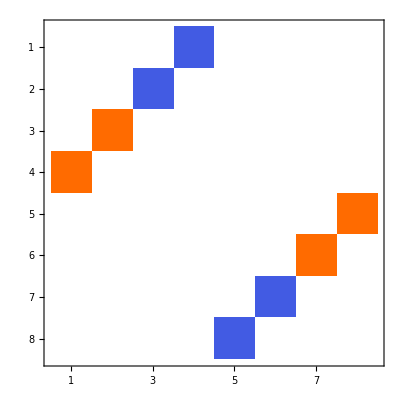

```mathematica
MatrixPlot[Im@matrep]
```

MatrixPlot can only handle real numbers, so Abs, Re or Im are needed to handle the imaginary factors.

The calculation of the matrix representation and its conversion to visible form may be done in one line:

```mathematica
MatrixRepresentation[opI[1,"x"].opI[2,"y"].opI[3,"z"]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

However there are some pitfalls in doing this..

#### a common pitfall

The line below looks OK. However the code sets the symbol matrep to the displayed form of the matrix representation, and not to the matrix itself:

```mathematica
matrep=MatrixRepresentation[opI[1,"x"].opI[2,"y"].opI[3,"z"]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

The symbol matrep is not a matrix or a SparseArray, but the display form of the matrix.

Multiplying two objects of this type does not give the expected result:

```mathematica
matrep.matrep
```

(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0).(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

To use the matrices in calculations, the MatrixForm must be calculated separately:

```mathematica
matrep=MatrixRepresentation[opI[1,"x"].opI[2,"y"].opI[3,"z"]]
%//MatrixForm
```

SparseArray[…]

(0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

```mathematica
matrep.matrep
%//MatrixForm
```

SparseArray[…]

(1/64 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/64 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/64 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/64 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/64 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/64 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64)

#### MatrixRepresentation with other bases

Any basis may be used for MatrixRepresentation. For example, the lines below calculate the matrix representation of the product operator I_(1x)I_(2y)I_(3+) in the eigenbasis of the scalar coupling operator I_1·I_2:

```mathematica
MatrixRepresentation[
opI[1,"x"].opI[2,"y"].opI[3,"z"],
Eigenbasis[opI[1].opI[2]]
]
%//MatrixForm//Chop
```

SparseArray[…]

(0 | 0 | 0.-0.125 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.+0.125 ⅈ | 0
0.+0.125 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.+0.125 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.125 ⅈ
0 | 0 | 0 | 0.-0.125 ⅈ | 0 | 0 | 0 | 0
0 | 0.-0.125 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.125 ⅈ | 0 | 0 | 0)

### VectorRepresentation

The vector representation of a Ket or a Bra in a given basis is calculated using VectorRepresentation. 
The output of VectorRepresentation is a SparseArray.

For example, this code provides the VectorRepresentation of a particular Ket in the ZeemanBasis, and visualizes the result:

```mathematica
SetSpinSystem[2];
VectorRepresentation[Ket["αα"]+Ket["αβ"],ZeemanBasis[]]
%//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SparseArray[…]

(1
0
1
0)

This code provides the matrix representation in the eigenbasis of an operator:

```mathematica
VectorRepresentation[Ket["αα"]+Ket["αβ"],Eigenbasis[opI["x"]]]
%//MatrixForm
```

SparseArray[…]

(1.
5.55112×10^-16
-0.707107
-0.707107)

## General spin operator routines

### CoherenceOrder

CoherenceOrder provides the coherence order of an operator

```mathematica
SetSpinSystem[4];
CoherenceOrder[opI[1,"-"].opI[2,"-"].opI[3,"+"].opI[4,"-"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

-2

If an operator contains a mixture of coherence orders, CoherenceOrder returns all of them:

```mathematica
CoherenceOrder[opI[1,"x"].opI[2,"y"].opI[3,"+"].opI[4,"z"]]
```

{-1,1,3}

The spins included in the coherence order calculation may be specified:

```mathematica
CoherenceOrder[{1,2},opI[1,"-"].opI[2,"-"].opI[3,"+"].opI[4,"-"]
]
```

-2

### OperatorNorm

The norm of an operator is the Frobenius norm of its matrix representation (square root of the sum of the square moduli of all matrix elements). OperatorNorm evaluates the norm of an operator,  in the current basis.

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
OperatorNorm[opI["x"]]
```

√2

### NormalizeOperator

NormalizeOperator sets the norm to 1 by dividing an operator by its norm, for example

```mathematica
SetSpinSystem[2];
NormalizeOperator[opI["x"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

(I_(1x)+I_(2x))/(√2)

#### using a norm different from 1

A second numerical argument may be used to set the norm of an operator to any desired value:

```mathematica
op=NormalizeOperator[opI["x"],10]
```

5 √2 (I_(1x)+I_(2x))

```mathematica
OperatorNorm[op]
```

10

If the second argument is another operator, the norm of the first operator is set to match the norm of the second operator:

```mathematica
op2=3opI[1,"x"]
OperatorNorm[op2]
op=NormalizeOperator[opI["x"],op2]
OperatorNorm[op]
```

3 I_(1x)

3

(3 (I_(1x)+I_(2x)))/(√2)

3

### OperatorAmplitude

OperatorAmplitude provides the answer to a question such as “how much of operator B is contained in operator A”. The general syntax for answering the question above is OperatorAmplitude[A→B].

Technically, if an operator A may be written as follows:
	A = b×B + C
where Tr{B^†C}=0, then the number b is the result of OperatorAmplitude[A→B]. We can say colloquially that operator A “contains” b × operator B.

For example, the instructions below show that the coefficient of the shift operator I^-in the operator I_y is i/2:

```mathematica
OperatorAmplitude[opI["y"]->opI["-"]]
```

ⅈ/2

This may be interpreted as saying that I_y contains (i/2)I^-.

Similarly, the line below shows how much of the shift operator product I_1^-I_2^+ is contained in the Cartesian product operator 2 I_(1y)I_(2y).

```mathematica
OperatorAmplitude[2opI[1,"y"].opI[2,"y"]->opI[1,"-"].opI[2,"+"]]
```

1/2

It is possible to calculate the amplitudes of several operators “contained inside” another operator at the same time, using the following syntax:

```mathematica
OperatorAmplitude[opI[1,"y"]->{opI[1,"-"],opI[1,"+"],opI[2,"z"]}]
```

{ⅈ/2,-ⅈ/2,0}

This means that the operator I_(1y) “contains” (i/2)I_1^-, and also (-i/2)I_1^-, but no I_(2z).

One must always be careful about the order of the operators in OperatorAmplitude. The opposite calculation gives a different result:

```mathematica
OperatorAmplitude[opI["x"]+3opI["y"]->opI["y"]]
```

3

```mathematica
OperatorAmplitude[opI["y"]->opI["x"]+3opI["y"]]
```

3/10

The last line indicates that the operator I_y may be written as (3/10)(I_x+3 I_y) + [orthogonal operators] - which is not obvious, but true!

### ExpressOperator

The full functionality of ExpressOperator is described in part 4 of the documentation. Briefly, ExpressOperator can be used to write a given spin operator in terms of sets of defined operators. A particularly useful form is ExpressOperator[op,CartesianProductOperatorBasis[]] which writes a general operator as a set of Cartesian product operators.

The example below expresses the operator I_1^+I_2^-I_3^+ as a superposition of Cartesian product operators:

```mathematica
SetSpinSystem[3];
ExpressOperator[opI[1,"+"].opI[2,"-"].opI[3,"+"],CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

I_(1x)•I_(2x)•I_(3x)+ⅈ (I_(1x)•I_(2x)•I_(3y))-ⅈ (I_(1x)•I_(2y)•I_(3x))+I_(1x)•I_(2y)•I_(3y)+ⅈ (I_(1y)•I_(2x)•I_(3x))-I_(1y)•I_(2x)•I_(3y)+I_(1y)•I_(2y)•I_(3x)+ⅈ (I_(1y)•I_(2y)•I_(3y))

### OperatorType

OperatorType may be applied to an operator to determine whether it is Hermitian, antiHermitian, Unitary, Normal, etc.

```mathematica
OperatorType[opI["x"]]
```

Hermitian

```mathematica
OperatorType[-I opI["x"]]
```

AntiHermitian

```mathematica
OperatorType[RotationOperator[{π/2,"x"}]]
```

Unitary

### Commutator

Commutator provides the commutator of two operators

```mathematica
SetSpinSystem[1];
Commutator[opI["x"],opI["y"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

I_(1x)•I_(1y)-I_(1y)•I_(1x)

This expression does not automatically simplify further. The commutation relationships of the angular momentum operators may be verified by calculating the matrix representations:

```mathematica
MatrixRepresentation[Commutator[opI["x"],opI["y"]]]==MatrixRepresentation[I opI["z"]]
```

True

An alternative method for simplification is to use ExpressOperator

```mathematica
ExpressOperator[Commutator[opI["x"],opI["y"]]]
```

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

ⅈ I_(1z)

### Secularize

Secularize removes non-secular components of an operator, defined according to various criteria.

#### Zeeman secularization

In the syntax below, the components of a coupling Hamiltonian that are non-secular with respect to a high-field Zeeman interaction, are removed. In this case it is assumed implicitly that all spins in the system are of the same isotopic type.

```mathematica
SetSpinSystem[2];
Secularize[ωsec opI[1,"z"].opI[2,"z"]+ωnonsec opI[1,"z"].opI[2,"x"] ]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

ωsec (I_(1z)•I_(2z))

Note that the non-secular second term in the operator has been removed.

In heteronuclear spin systems, it is often useful to secularize an operator by assuming a heteronuclear Zeeman interaction with very different Larmor frequencies for the two spin species. In the example below, a four-spin system is defined, with two I-spins and two S-spins. A set of coupling Hamiltonians is secularized with respect to these two groups of spins.

```mathematica
SetSpinSystem[4];
Ispins={1,2};
Sspins={3,4};
Secularize[
2π Subscript[J, 12] opI[1].opI[2]+2π Subscript[J, 13] opI[1].opI[3]+2π Subscript[J, 14] opI[1].opI[4]+
2π Subscript[J, 23] opI[2].opI[3]+2π Subscript[J, 24] opI[2].opI[4]+2π Subscript[J, 34] opI[3].opI[4],
{Ispins,Sspins}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},Sorted→CoherenceOrder].

π (I_1^-•I_2^+) J_12+π (I_1^+•I_2^-) J_12+2 π (I_(1z)•I_(2z)) J_12+2 π (I_(1z)•I_(3z)) J_13+2 π (I_(1z)•I_(4z)) J_14+2 π (I_(2z)•I_(3z)) J_23+2 π (I_(2z)•I_(4z)) J_24+π (I_3^-•I_4^+) J_34+π (I_3^+•I_4^-) J_34+2 π (I_(3z)•I_(4z)) J_34

Note that only the zz terms remain between pairs of spins of different isotopic type.

#### Secularization using an arbitrary Hamiltonian

Secularization may also be performed using an arbitrary Hamiltonian. The syntax is Secularize[op,H0]. The routine expresses the operator op in the eigenbasis of the Hamiltonian H0, and then removes off-diagonal elements between non-degenerate eigenstates of H0.

In the examples below, a scalar coupling interaction is secularized against a Zeeman interaction for two spins-1/2, using an explicit Zeeman Hamiltonian definition.

In the first case, the chemical shifts of the two spins are identical. Secularization has no effect in this case. This corresponds to magnetic equivalence.

```mathematica
SetSpinSystem[2];
Secularize[2π 10 opI[1].opI[2],
2π 100 opI[1,"z"]+2π 100 opI[2,"z"]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

31.4159 (I_1^-•I_2^+)+31.4159 (I_1^+•I_2^-)+62.8319 (I_(1z)•I_(2z))

In the case below, a large chemical shift difference is introduced. Secularization leaves only the zz-terms. This is the weak coupling limit.

```mathematica
SetSpinSystem[2];
Secularize[2π 10 opI[1].opI[2],
2π 100 opI[1,"z"]-2π 100 opI[2,"z"]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

62.8319 (I_(1z)•I_(2z))

A numerical threshold is used to determine whether two eigenvalues are degenerate or not. By default this is equal to $ChopThreshold, which is a very small number (see “global settings” in Part 1 of the documentation). Hence the default syntax Secularize[op,H0] essentially uses exact degeneracy as a secularization criterion. 
However, it is also possible to specify the degeneracy threshold using a third numerical argument for Secularize. The example below is the same as the one above, but using a large threshold of 200 Hz for the degeneracy criterion. The removal of off-diagonal elements is thereby suppressed.

```mathematica
SetSpinSystem[2];
Secularize[2π 10 opI[1].opI[2],
2π 100 opI[1,"z"]-2π 100 opI[2,"z"],
2π 200
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

31.4159 (I_1^-•I_2^+)+31.4159 (I_1^+•I_2^-)+62.8319 (I_(1z)•I_(2z))

### Operator

A general way of defining an operator in SpinDynamica is to use the routine Operator together with the matrix representation in a certain basis.

An operator defined this way is basis-independent. The stored information may be used to derive the matrix representation of the operator in any desired basis.

#### defining a general Operator

The lines below define the symbol op to be an operator with a defined 2×2 matrix representation in the Zeeman basis, for a single spin-1/2:

```mathematica
SetSpinSystem[1];
op1=Operator[{{1,0},{I,0}},ZeemanBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Operator[<<..>>, OperatorType→None ]

#### precalculation of a symbolic operator

Operator may also be used to precalculate and store the matrix representation of a symbolic operator, for example

```mathematica
SetSpinSystem[3];
op2=Operator[opI[1,"x"].opI[{2,3},"y"]+π opI[3,"+"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

Operator[<<..>>, OperatorType→None ]

This allows complex symbolic operators to be stored as a numerical matrix representation in a defined basis. This can be useful for speeding up calculations.

#### MatrixRepresentation of an Operator

The matrix representation of the resulting operator may be obtained as usual:

```mathematica
SetSpinSystem[1];
MatrixRepresentation[op1]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

(1 | 0
ⅈ | 0)

The matrix representation may be obtained in a different basis, if desired:

```mathematica
MatrixRepresentation[op1,Eigenbasis[opI["x"]]]//MatrixForm
```

(0.5-0.5 ⅈ | -0.5+0.5 ⅈ
-0.5-0.5 ⅈ | 0.5+0.5 ⅈ)

#### applying an Operator to a Ket

The operator may be applied to Ket:

```mathematica
op1[Ket["α"]]
```

ⅈ |β⟩+|α⟩

#### OperatorType

By default Operator estimates the OperatorType on execution, by examining the symmetry of the MatrixRepresentation. Some examples follow:

```mathematica
SetSpinSystem[1];
Operator[{{0,1},{1,0}}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Operator[<<..>>, OperatorType→Hermitian ]

```mathematica
Operator[{{0,I},{-I,0}}]
```

Operator[<<..>>, OperatorType→Hermitian ]

```mathematica
Operator[{{I,0},{0,-I}}]
```

Operator[<<..>>, OperatorType→AntiHermitian ]

The OperatorType is used internally to implement specific algorithms for certain types of operators.

#### Basis

The basis in which an operator is originally defined may be extracted by applying Basis:

```mathematica
SetSpinSystem[2];
SetBasis[SingletTripletBasis[]];
op=Operator[{{0,1,1,0},{1,0,0,1},{0,1,1,0},{0,1,1,0}}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SetBasis::set: the state basis has been set to SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Operator[<<..>>, OperatorType→None ]

```mathematica
SetBasis[ZeemanBasis[]]
```

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
Basis[op]
```

SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic]

```mathematica
MatrixRepresentation[op]//MatrixForm
```

(0 | -1/(√2) | 1/(√2) | 1
0 | 0 | 0 | 0
√2 | 1 | 1 | 0
1 | 1/(√2) | 1/(√2) | 0)

### NDiagonalize

NDiagonalize may be used to convert any operator into a form which is diagonalized in a specified basis (or in the current basis, by default). The output of NDiagonalize is a special form of Operator which may be used just like any other operator. Certain routines run faster when operators have been pre-converted into a diagonalized form.

#### example

```mathematica
SetSpinSystem[2];
op=NDiagonalize[2 opI[1,"x"].opI[2,"y"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Operator[DiagonalizedForm[<<..{4,4}..>>], OperatorType→"Hermitian"]

```mathematica
MatrixRepresentation[op]//MatrixForm
```

(0 | 0 | 0 | 0.-0.5 ⅈ
0 | 0 | 0.-0.5 ⅈ | 0
0 | 0.+0.5 ⅈ | 0 | 0
0.+0.5 ⅈ | 0 | 0 | 0)

#### output of NDiagonalize

The output of NDiagonalize, when applied to an operator,  has the form Operator[{X,evals,Xinv}, basis...] where evals is the vector of eigenvalues, X is a matrix whose columns are the eigenvectors of the matrix representation of the operator in the basis basis, and Xinv is the inverse of X. The elements {X,evals,Xinv} may be inspected by applying First to the output of NDiagonalize

```mathematica
{X,evals,Xinv}=First[op]
```

{SparseArray[…],{0.5,0.5,-0.5,-0.5},SparseArray[…]}

```mathematica
MatrixForm[X]
evals
MatrixForm[Xinv]
```

(0 | 0.-0.707107 ⅈ | 0 | 0.+0.707107 ⅈ
0.707107 | 0 | 0.707107 | 0
0.+0.707107 ⅈ | 0 | 0.-0.707107 ⅈ | 0
0 | 0.707107 | 0 | 0.707107)

{0.5,0.5,-0.5,-0.5}

(0 | 0.707107 | 0.-0.707107 ⅈ | 0
0.+0.707107 ⅈ | 0 | 0 | 0.707107
0 | 0.707107 | 0.+0.707107 ⅈ | 0
0.-0.707107 ⅈ | 0 | 0 | 0.707107)

#### NDiagonalize in different bases

The basis used for NDiagonalize may be specified explicitly. Although the form of the matrices X and Xinv depend on the basis, the operator output of NDiagonalize is basis independent:

```mathematica
SetSpinSystem[2];
op1=NDiagonalize[opI["x"],ZeemanBasis[]]
op2=NDiagonalize[opI["x"],SingletTripletBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Operator[DiagonalizedForm[<<..{4,4}..>>], OperatorType→"Hermitian"]

Operator[DiagonalizedForm[<<..{4,4}..>>], OperatorType→"Hermitian"]

```mathematica
Basis[op1]
```

ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic]

```mathematica
Basis[op2]
```

SingletTripletBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic]

Although the internal representations are different, the two diagonalized operators have identical matrix representations in a common basis:

```mathematica
MatrixRepresentation[op1,ZeemanBasis[]]//MatrixForm
MatrixRepresentation[op2,ZeemanBasis[]]//MatrixForm
```

(0 | 0.5 | 0.5 | 0
0.5 | 0 | 0 | 0.5
0.5 | 0 | 0 | 0.5
0 | 0.5 | 0.5 | 0)

(0. | 0.5 | 0.5 | 0.
0.5 | 0. | 0. | 0.5
0.5 | 0. | 0. | 0.5
0. | 0.5 | 0.5 | 0.)

#### restrictions

NDiagonalize may only be applied to operators with numeric matrix representations

```mathematica
ω=.;
NDiagonalize[ω opI[1,"x"].opI[2,"y"]]
```

NDiagonalize::notnummat: NDiagonalize cannot be applied to a non-numeric matrix. Check that all symbols have numeric values.

$Failed

```mathematica
ω=2π 100;
NDiagonalize[ω opI[1,"x"].opI[2,"y"]]
```

Operator[DiagonalizedForm[<<..{4,4}..>>], OperatorType→"Hermitian"]

## Specific spin operators

### Spin angular momentum operators: opI

The functionality of opI was described in part 1 of this documentation.

### UnityOperator and NullOperator

UnityOperator and NullOperator are defined within SpinDynamica:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

```mathematica
UnityOperator[]
```

𝟙

```mathematica
UnityOperator[].Ket["αα"]
```

|αα⟩

```mathematica
NullOperator[]
```

𝕆

```mathematica
NullOperator[].Ket["αα"]
```

0

```mathematica
Bra["αα"].NullOperator[]
```

0

### Rotation operators: opR

Rotation operators are described in SpinDynamica by the symbol RotationOperator and its synonym opR.

#### syntax

The syntax opR[<spin label>,{angle,axis}] rotates a single spin about a specified axis, for example

```mathematica
SetSpinSystem[3];
opR[1,{π/2,"x"}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

R_(1x)(π/2)

This represents a rotation of spin #1 by 90° about the x-axis.

A list of spins defines identical rotations for all spins in the list:

```mathematica
Ispins={1,2};
opR[Ispins,{π/2,"x"}]
```

R_(1x)(π/2)•R_(2x)(π/2)

The absence of a spin label implies a product of identical rotations for all spins:

```mathematica
opR[{π/2,"x"}]
```

R_(1x)(π/2)•R_(2x)(π/2)•R_(3x)(π/2)

If a number is used for the axis specification, an axis in the xy-plane is implied. This is represented in SpinDynamica as a sandwich of rotations about orthogonal axes:

```mathematica
opR[1,{π/2,π/4}]
```

R_(1z)(π/4)•R_(1x)(π/2)•R_(1z)(-π/4)

The rotation angle and axis may also be specified using polar angles, as follows:

```mathematica
opR[1,{ξ,{θ,ϕ}}]
```

R_(1z)(ϕ)•R_(1y)(θ)•R_(1z)(ξ)•R_(1y)(-θ)•R_(1z)(-ϕ)

Euler angles may also be used, as follows:

```mathematica
opR[1,{α,β,γ}]
```

R_(1z)(α)•R_(1y)(β)•R_(1z)(γ)

#### MatrixRepresentation of rotation operators

The matrix representations of rotation operators are obtained through the application of MatrixRepresentation:

```mathematica
SetSpinSystem[1];
MatrixRepresentation[opR[{π/2,"x"}]]//MatrixForm
MatrixRepresentation[opR[{α,β,γ}]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))

(ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2] | -ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]
ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2] | ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2])

The matrix representations may also be generated for higher spin quantum numbers:

```mathematica
SetSpinSystem[{{"I",1}}];
MatrixRepresentation[opR[{π/2,"x"}]]//MatrixForm
MatrixRepresentation[opR[{α,β,γ}]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{I,1}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,1}},BasisLabels→Automatic].

(1/2 | -ⅈ/(√2) | -1/2
-ⅈ/(√2) | 0 | -ⅈ/(√2)
-1/2 | -ⅈ/(√2) | 1/2)

(ⅇ^(-ⅈ α-ⅈ γ) (1/2+Cos[β]/2) | -(ⅇ^(-ⅈ α) Sin[β])/(√2) | ⅇ^(-ⅈ α+ⅈ γ) (1/2-Cos[β]/2)
(ⅇ^(-ⅈ γ) Sin[β])/(√2) | Cos[β] | -(ⅇ^(ⅈ γ) Sin[β])/(√2)
ⅇ^(ⅈ α-ⅈ γ) (1/2-Cos[β]/2) | (ⅇ^(ⅈ α) Sin[β])/(√2) | ⅇ^(ⅈ α+ⅈ γ) (1/2+Cos[β]/2))

### Irreducible spherical tensor operators: opT

Irreducible spherical tensor operators (ISTOs) are widely used in magnetic resonance theory. They are sets of operators which span irreducible representations of the full rotation group.

In SpinDynamica, the general syntax for a spherical tensor operator is opT[spins,{rank,component}]. If the argument spins is omitted, a sum is taken over all spins in the current SpinSystem.

#### single spin-1/2

A single spin I can support an ISTOs with ranks from 0 up to 2I.

Here are examples for a single spin-1/2:

```mathematica
SetSpinSystem[1]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

```mathematica
opT[1,{0,0}]
```

𝟙

```mathematica
Table[opT[1,{1,m}],{m,-1,1}]
```

{I_1^-/(√2),I_(1z),-I_1^+/(√2)}

A single spin-1/2 cannot support an ISTO of rank more than 1:

```mathematica
opT[1,{2,2}]
```

𝕆

#### higher spins

Here are examples for a single spin-3/2:

```mathematica
SetSpinSystem[{{"I",3/2}}]
```

SetSpinSystem::set: the spin system has been set to {{I,3/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{I,3/2}},BasisLabels→Automatic].

```mathematica
opT["I",{0,0}]
```

𝟙

```mathematica
Table[opT["I",{1,m}],{m,-1,1}]
```

{I^-/(√2),I_z,-I^+/(√2)}

```mathematica
Table[opT["I",{2,m}],{m,-2,2}]//Simplify
```

{1/2 (I^-•I^-),1/2 (I^-•I_z+I_z•I^-),-(I⃗•I⃗-3 (I_z•I_z))/(√6),1/2 (-(I^+•I_z)-I_z•I^+),1/2 (I^+•I^+)}

The higher rank STOs are evaluated using the Wigner-Eckart theorem and expressed using their matrix representations:

```mathematica
opT["I",{3,0}]
```

opT::highλ: Spherical tensor operators of high rank are calculated using the Wigner-Eckart theorem and provided in the form of Operator. Explicit expressions may be constructed by applying ExpressOperator. This message appears only once.

Operator[<<..>>, OperatorType→Hermitian ]

Explicit expressions may be obtained by using ExpressOperator

```mathematica
ExpressOperator[opT["I",{3,0}],ShiftAndZOperatorBasis[]]
```

1/3 √5 (I_z•I_z•I_z)-(41 I_z)/(12 √5)

#### multiple spins

An ISTO may also involve several spins.

For example, these are the five rank-2 ISTOs for 2 coupled spins-1/2:

```mathematica
SetSpinSystem[2];
Table[opT[{1,2},{2,m}],{m,-2,2}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

{1/2 (I_1^-•I_2^-),1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6),1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+),1/2 (I_1^+•I_2^+)}

This is the rank-0 (isotropic) ISTO for 2 coupled spins-1/2:

```mathematica
opT[{1,2},{0,0}]
```

-(I_1^-•I_2^++I_1^+•I_2^-+2 (I_(1z)•I_(2z)))/(2 √3)

These are the rank-1 ISTOs involving two spins-1/2:

```mathematica
Table[opT[{1,2},{1,m}],{m,-1,1}]//Simplify
```

{1/2 (-(I_1^-•I_(2z))+I_(1z)•I_2^-),(I_1^-•I_2^+-I_1^+•I_2^-)/(2 √2),1/2 (-(I_1^+•I_(2z))+I_(1z)•I_2^+)}

These are the rank-3 ISTOs for 3 coupled spins - 1/2:

```mathematica
SetSpinSystem[3];
Table[opT[{1,2,3},{3,m}],{m,-3,3}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

{(I_1^-•I_2^-•I_3^-)/(2 √2),(I_1^-•I_2^-•I_(3z)+I_1^-•I_(2z)•I_3^-+I_(1z)•I_2^-•I_3^-)/(2 √3),-(I_1^-•I_2^-•I_3^++I_1^-•I_2^+•I_3^--4 (I_1^-•I_(2z)•I_(3z))+I_1^+•I_2^-•I_3^--4 (I_(1z)•I_2^-•I_(3z))-4 (I_(1z)•I_(2z)•I_3^-))/(2 √30),-(I_1^-•I_2^+•I_(3z)+I_1^-•I_(2z)•I_3^++I_1^+•I_2^-•I_(3z)+I_1^+•I_(2z)•I_3^-+I_(1z)•I_2^-•I_3^++I_(1z)•I_2^+•I_3^--4 (I_(1z)•I_(2z)•I_(3z)))/(2 √10),(I_1^-•I_2^+•I_3^++I_1^+•I_2^-•I_3^++I_1^+•I_2^+•I_3^--4 (I_1^+•I_(2z)•I_(3z))-4 (I_(1z)•I_2^+•I_(3z))-4 (I_(1z)•I_(2z)•I_3^+))/(2 √30),(I_1^+•I_2^+•I_(3z)+I_1^+•I_(2z)•I_3^++I_(1z)•I_2^+•I_3^+)/(2 √3),-(I_1^+•I_2^+•I_3^+)/(2 √2)}

#### multiple ISTO solutions

In some cases, there are several ISTOs of the same rank and component index. The routine will report this, and return a list of all solutions:

```mathematica
SetSpinSystem[3];
opT[{1,2,3},{2,0}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

opT::multiple: There are 2 operators with this specification. A list of all possibilities has been returned. Specify a single operator using the form opT[interactions,{Lam,M},index] where index is an integer.

{(2 (I_1^-•I_2^+•I_(3z))+I_1^-•I_(2z)•I_3^+-2 (I_1^+•I_2^-•I_(3z))-I_1^+•I_(2z)•I_3^--I_(1z)•I_2^-•I_3^++I_(1z)•I_2^+•I_3^-)/(4 √3),1/4 (I_1^-•I_(2z)•I_3^+-I_1^+•I_(2z)•I_3^-+I_(1z)•I_2^-•I_3^+-I_(1z)•I_2^+•I_3^-)}

#### Normalize

By default, the ISTOs are not normalized. They may be normalized automatically by using the option Normalize→True

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
opT[{1,2},{2,0}]
OperatorNorm[%]
```

-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6)

1/2

```mathematica
opT[{1,2},{2,0},Normalize->True]
OperatorNorm[%]
```

-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(√6)

1

#### SphericalTensorIndices

The spherical tensor content of any operator may be derived by applying SphericalTensorIndices. The example below shows that in a 3-spin-1/2 system, the operator I_(1z)I_(2z)I_(3z)contains spherical components with {rank,component} values {1,0} and {3,0}.

```mathematica
SetSpinSystem[3]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

```mathematica
SphericalTensorIndices[opI[1,"z"].opI[2,"z"].opI[3,"z"]]
```

{{1,0},{3,0}}

### SingleTransitionOperator

A single transition operator (also known as a fictitious spin-1/2 operator) refer to operators involving only 2 states in a multistate system. The classic references to single transition operators are S. Vega, J. Chem. Phys. 68, 5518-55127 (1978) and A. Wokaun and R. R. Ernst, J. Chem. Phys. 67, 1752-1758 (1977).

For example, the operator I_x^(rs)is defined as 1/2(|r><s|+|r><s|).

In SpinDynamica, single operators may be written in the form SingleTransitionOperator[{ketr,kets},μ], where μ can be “x”, “y”, “z”, “+“ or “-“.

The following example defines a x-single-transition operator between the singlet state and the central triplet state in a 2-spin-1/2 system:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
BasisKets[SingletTripletBasis[]]
```

{(-|βα⟩+|αβ⟩)/(√2),|αα⟩,(|βα⟩+|αβ⟩)/(√2),|ββ⟩}

```mathematica
stop=SingleTransitionOperator[{1,3},"x",SingletTripletBasis[]]
```

-(|βα⟩.<βα|)/2+(|αβ⟩.<αβ|)/2

```mathematica
MatrixRepresentation[stop, SingletTripletBasis[]]//MatrixForm
```

(0 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### using Kets

The example below shows the single transition x-operator for two defined kets:

```mathematica
SetSpinSystem[2];
SingleTransitionOperator[{Ket["αα"],Ket["αβ"]},"x"]
MatrixRepresentation[%]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

(|αβ⟩.<αα|)/2+(|αα⟩.<αβ|)/2

(0 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | 0)

The example below shows the single transition z - operator :

```mathematica
SingleTransitionOperator[{Ket["αα"],Ket["αβ"]},"z"]
MatrixRepresentation[%]//MatrixForm
```

-(|αβ⟩.<αβ|)/2+(|αα⟩.<αα|)/2

(1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | 0)

#### using BasisLabels

Single-transition operators may also be generated by using the BasisLabels to define the states. The example below defines the single-transition x-operator between the states with labels 3 and 4 in the ZeemanBasis:

```mathematica
op=SingleTransitionOperator[{{3,4},ZeemanBasis[]},"x"];
MatrixRepresentation[op]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/2
0 | 0 | 1/2 | 0)

If the basis is omitted, the current basis is assumed

```mathematica
op=SingleTransitionOperator[{1,2},"x"];
MatrixRepresentation[op]//MatrixForm
```

(0 | 1/2 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### commutation relationships

The commutation relationships of the single-transition operators may be verified by evaluating the matrix representations:

```mathematica
Commutator[
SingleTransitionOperator[{3,4},"x"],
SingleTransitionOperator[{3,4},"y"]
]
```

-1/2 ⅈ (|ββ⟩.<ββ|-|αβ⟩.<αβ|)

```mathematica
MatrixRepresentation@Commutator[
SingleTransitionOperator[{3,4},"x"],
SingleTransitionOperator[{3,4},"y"]
]==
MatrixRepresentation[I SingleTransitionOperator[{3,4},"z"]
]
```

True

```mathematica
MatrixRepresentation@Commutator[
SingleTransitionOperator[{2,3},"x"],
SingleTransitionOperator[{3,4},"x"]
]==
MatrixRepresentation[(I/2) SingleTransitionOperator[{2,4},"y"]
]
```

True

### CoherenceOperator

A coherence operator is defined as |r><s| where |r> and |s> are kets of a given basis. This is implemented in SpinDynamica by CoherenceOperator[{r,s},basis]. If basis is missing, the current basis is used.

The following example defines a coherence operator between the singlet state and the central triplet state in a 2-spin-1/2 system:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

```mathematica
BasisKets[SingletTripletBasis[]]
```

{(-|βα⟩+|αβ⟩)/(√2),|αα⟩,(|βα⟩+|αβ⟩)/(√2),|ββ⟩}

```mathematica
STcohop=CoherenceOperator[{1,3},SingletTripletBasis[]]
```

1/2 (-|βα⟩.<βα|-|βα⟩.<αβ|+|αβ⟩.<βα|+|αβ⟩.<αβ|)

```mathematica
MatrixRepresentation[STcohop, SingletTripletBasis[]]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The coherence operator may be expressed in terms of other operators as follows:

```mathematica
ExpressOperator[STcohop,CartesianProductOperatorBasis[]]
```

-ⅈ (I_(1x)•I_(2y))+ⅈ (I_(1y)•I_(2x))+(I_(1z))/2-(I_(2z))/2

#### using Kets

The example below shows the single transition x-operator for two defined kets:

```mathematica
SetSpinSystem[2];
SingleTransitionOperator[{Ket["αα"],Ket["αβ"]},"x"]
MatrixRepresentation[%]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

(|αβ⟩.<αα|)/2+(|αα⟩.<αβ|)/2

(0 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | 0)

The example below shows the single transition z - operator :

```mathematica
SingleTransitionOperator[{Ket["αα"],Ket["αβ"]},"z"]
MatrixRepresentation[%]//MatrixForm
```

-(|αβ⟩.<αβ|)/2+(|αα⟩.<αα|)/2

(1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | 0)

#### commutation relationships

The commutation relationships of the single-transition operators may be verified by evaluating the matrix representations:

```mathematica
ST13x=SingleTransitionOperator[{1,3},"x",SingletTripletBasis[]]
```

-(|βα⟩.<βα|)/2+(|αβ⟩.<αβ|)/2

```mathematica
ST13y=SingleTransitionOperator[{1,3},"y",SingletTripletBasis[]]
```

(ⅈ |βα⟩.<αβ|)/2-(ⅈ |αβ⟩.<βα|)/2

```mathematica
ST13z=SingleTransitionOperator[{1,3},"z",SingletTripletBasis[]]
```

-(|βα⟩.<αβ|)/2-(|αβ⟩.<βα|)/2

```mathematica
Commutator[ST13x,ST13y]/.{0->NullOperator[]}
```

-1/2 ⅈ (|βα⟩.<αβ|+|αβ⟩.<βα|)

```mathematica
MatrixRepresentation[
Commutator[ST13x,ST13y]/.{0->NullOperator[]}
]==MatrixRepresentation[I ST13z]
```

True

### PopulationOperator

A population operator is defined as |r><r| where |r> is a ket of a given basis. This is implemented in SpinDynamica by PopulationOperator[r,basis].  If basis is missing, the current basis is used.

The following example defines a population operator for the singlet state in a 2-spin-1/2 system:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

```mathematica
BasisKets[SingletTripletBasis[]]
```

{(-|βα⟩+|αβ⟩)/(√2),|αα⟩,(|βα⟩+|αβ⟩)/(√2),|ββ⟩}

```mathematica
singletpopop=PopulationOperator[1,SingletTripletBasis[]]
```

1/2 (|βα⟩.<βα|-|βα⟩.<αβ|-|αβ⟩.<βα|+|αβ⟩.<αβ|)

```mathematica
MatrixRepresentation[singletpopop, SingletTripletBasis[]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The population operator may be expressed in terms of other operators as follows:

```mathematica
ExpressOperator[singletpopop,CartesianProductOperatorBasis[]]
```

-(I_(1x)•I_(2x))-I_(1y)•I_(2y)-I_(1z)•I_(2z)+𝟙/4

### SpinPermutationOperator

SpinPermutationOperator is the operator for a permutation of spins. The general syntax is SpinPermutationOperator[{j,k,l,..m}] which indicates a cyclic permutation of spins, i.e. j→k, k→l, .., m→j.

The example below shows the effect of four successive cyclic permutations of 4 spins, acting on a Ket:

```mathematica
SetSpinSystem[4];
SpinPermutationOperator[{1,2,3,4}][Ket["αβαα"]]
SpinPermutationOperator[{1,2,3,4}][%]
SpinPermutationOperator[{1,2,3,4}][%]
SpinPermutationOperator[{1,2,3,4}][%]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

|ααβα⟩

|αααβ⟩

|βααα⟩

|αβαα⟩

SpinPermutationOperator[{j,k}] leads to the exchange of spins j and k:

```mathematica
SpinPermutationOperator[{1,2}][Ket["αβαα"]]
```

|βααα⟩

Successive permutations may be specified using the syntax SpinPermutationOperator[{..permutation2, permutation1}] where the right-most permutation is applied first. For example:

```mathematica
SpinPermutationOperator[{{3,4},{2,3}}][Ket["αβαα"]]
```

|αααβ⟩

The matrix representation of a SpinPermutationOperator is calculated in the usual way:

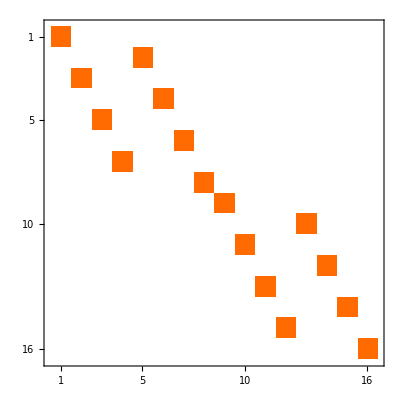

```mathematica
MatrixRepresentation[SpinPermutationOperator[{1,2,3}]]//MatrixPlot
```